```mathematica
(*only with sigma+*)
(*figure3a*)
(*magnetic filed*)

Clear["Global`*"]
(*The internal coupling between two molecules with sigma+ microwave shielding W=Subscript[H, 0] 1+Subscript[H, 0] 2+Subscript[H, int]*)
(*The basis of two microwave-shielded molecules in rotation frame |+,+>,|+,Subscript[e, 0]>,|+,Subscript[e, -1]>,|+,- >,|-,Subscript[e, 0]>,|-,Subscript[e, -1]>,|-,- >;|+> =a|g>+b|Subscript[e, 1]>,|- > =a|Subscript[e, 1]>-b|g>*)
(*The Hamiltion can be written as 7×7 matrix*)

ome=(om^2+de^2)^(1/2);(*om is rabi frequency,de is blue detuning*)
a=Sqrt[(1-de/ome)/2];
b=Sqrt[(1+de/ome)/2];
(*dipolar interaction V*)
c=a^2-b^2;
Z20=1/(4π*√6)*({{-2*a^2*b^2, 0, 0, -√2 a*b*c, 0, 0, 2*a^2*b^2}, {0, 2*a^2, 0, 0, -2*a*b, 0, 0}, {0, 0, -a^2, 0, 0, a*b, 0}, {-√2 a*b*c, 0, 0, -c^2, 0, 0, √2 a*b*c}, {0, -2*a*b, 0, 0, 2*b^2, 0, 0}, {0, 0, a*b, 0, 0, -b^2, 0}, {2*a^2*b^2, 0, 0, √2 a*b*c, 0, 0, -2*a^2*b^2}});
Z21=1/(4π*√2)*({{0, √2 a^2*b, 0, 0, -√2 a*b^2, 0, 0}, {0, 0, -a^2, 0, 0, a*b, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, a*c, 0, 0, -b*c, 0, 0}, {0, 0, a*b, 0, 0, -b^2, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, -√2 a^2*b, 0, 0, √2 a*b^2, 0, 0}});
Z22=-1/(4π)*({{0, 0, √2 a^2*b, 0, 0, -√2 a*b^2, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, a*c, 0, 0, -b*c, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, -√2 a^2*b, 0, 0, √2 a*b^2, 0}});

Hint=-8 √(2/15)π^(3/2)d^2/(4π*ep*r^3)((-1)^2 SphericalHarmonicY[2,-2,t,p]*Z22+(-1)^1 SphericalHarmonicY[2,-1,t,p]*Z21+SphericalHarmonicY[2,0,t,p]*Z20+(-1)^-1 SphericalHarmonicY[2,1,t,p]*(-ConjugateTranspose[Z21])+
(-1)^-2 SphericalHarmonicY[2,2,t,p]*ConjugateTranspose[Z22]);
(*two single shielding molecule Subscript[H, 0] 1+Subscript[H, 0] 2*)
e1=0;
e2=1/2*(de-ome);
e3=1/2*(de-ome);
e4=-ome;
e5=1/2*(de-3*ome);
e6=1/2*(de-3*ome);
e7=-2*ome;
ee={e1,e2,e3,e4,e5,e6,e7};

(*the total Hamiltionian*)
W=DiagonalMatrix[ee]+Hint;
(*The first derivative of the Hamiltonian*)
Vr=D[W,r];
Vt=D[W,t];
Vp=Simplify[D[W,p]/Sin[t]];

(*demensionless*)
  eps0=8.854187817*10^(-12);(*permittivity of vacuum*)
  debai=3.33564*10^(-30);(*Deby*)
  a0=0.529*10^(-10);(*Bohr radius*)
  hbar=1.054*10^(-34);(*Planck constant*)
  M=155.8952/(6.02*10^23)*10^(-3);(*the mass of NaCs*)

  l0=1000*a0;(*length unit*)
  energy0=(debai^2/eps0)/l0^3;(*energy unit*)
  f0=energy0/hbar;
  ad=d^2*M*debai^2/(12*Pi*hbar^2*eps0)/l0;(*dipolar length*)


(*input parameter*)
om=(2*Pi)*10*10^6*hbar/energy0;
de=-(2*Pi)*10*10^6*hbar/energy0;(*Ω=Δ=10*2πMHZ*)
d=4.75;(*dipole momentum*)

ep=1;
p=0;(*ϕ*)

rmin=500*a0/l0;

rmax=2000*a0/l0;
dr=0.001;


dt=Pi/10;
tmin=-Pi;
tmax=Pi;
tval=Table[i,{i,tmin,tmax,dt}];(*θ*)
rval=Table[i,{i,rmin,rmax,dr}];(*r*)
VVr=Table[Vr,{r,rmin,rmax,dr},{t,tmin,tmax,dt}];
VVt=Table[Vt,{r,rmin,rmax,dr},{t,tmin,tmax,dt}];
VVp=Table[Vp,{r,rmin,rmax,dr},{t,tmin,tmax,dt}];
  VV=Table[W,{r,rmin,rmax,dr},{t,tmin,tmax,dt}];


(*diagonalization the Hamiltonian W*)
VVV=Table[Eigensystem[VV[[i,j]]],{i,1,Length[rval]},{j,1,Length[tval]}];
V=Table[Max[VVV[[i,j,1]]],{i,1,Length[rval]},{j,1,Length[tval]}];(*highest eigenvalue V(r,θ)*)
PP=Table[Flatten[Position[#,Max@#]&@VVV[[i,j,1]]],{i,1,Length[rval]},{j,1,Length[tval]}];
NN=ConstantArray[Table[ll,{ll,1,7}],{Length[rval],Length[tval]}];
l=Table[Drop[NN[[i,j]],PP[[i,j]]],{i,1,Length[rval]},{j,1,Length[tval]}];
PPP=Table[VVV[[i,j,2,PP[[i,j]]]],{i,1,Length[rval]},{j,1,Length[tval]}];(*the highest eigenstate |Ϛ>*)


(*Magnetic field B in 3D spherical coordinate with Bϕ=0*)
Br=Im[Table[Total[Table[Dot[PPP[[i,j]],VVt[[i,j]],Transpose[VVV[[i,j,2,l[[i,j,n]]]]]]*Dot[Transpose[VVV[[i,j,2,l[[i,j,n]]]]],VVp[[i,j]],Transpose[PPP[[i,j]]]]/((V[[i,j]]-VVV[[i,j,1,l[[i,j,n]]]])^2),{n,1,6}]]*(-2/(rval[[i]]^2)),{i,1,Length[rval]},{j,1,Length[tval]}]];
Bt=Im[Table[Total[Table[Dot[PPP[[i,j]],VVp[[i,j]],Transpose[VVV[[i,j,2,l[[i,j,n]]]]]]*Dot[Transpose[VVV[[i,j,2,l[[i,j,n]]]]],VVr[[i,j]],Transpose[PPP[[i,j]]]]/((V[[i,j]]-VVV[[i,j,1,l[[i,j,n]]]])^2),{n,1,6}]]*(-2/(rval[[i]])),{i,1,Length[rval]},{j,1,Length[tval]}]];
(*Magnetic field B in 3D rectangular coordinate with By=0*)
Bz=Table[Br[[i]]*Cos[tval]-Bt[[i]]*Sin[tval],{i,1,Length[rval]}];
Bx=Table[Br[[i]]*Sin[tval]+Bt[[i]]*Cos[tval],{i,1,Length[rval]}];
BB=Table[{Bx[[i,j,1]],Bz[[i,j,1]]},{i,1,Length[rval]},{j,1,Length[tval]}];

X=Table[rval[[i]]*Sin[tval][[j]],{i,1,Length[rval]},{j,1,Length[tval]}];
Z=Table[rval[[i]]*Cos[tval][[j]],{i,1,Length[rval]},{j,1,Length[tval]}];
```

```mathematica
SFl=ListLinePlot[{Table[{rval[[i]]/ad*10^3,Bt[[i,16,1]]*ad^2/10^4},{i,650,Length[rval]}],Table[{rval[[i]]/ad*10^3,Br[[i,16,1]]*ad^2/10^4},{i,650,Length[rval]}],Table[{rval[[i]]/ad*10^3,Bt[[i,21,1]]*ad^2/10^4},{i,650,Length[rval]}],Table[{rval[[i]]/ad*10^3,Br[[i,21,1]]*ad^2/10^4},{i,650,Length[rval]}],Table[{R/ad*10^3,i},{i,-5,2,0.01}]},
PlotRange->{{3.46,6.04},{-5,2}},
PlotStyle->{Directive[Red,Thickness[0.005]],Directive[Red,Thickness[0.005],Dashing[0.03]],Directive[Blue,Thickness[0.005],DotDashed],Directive[Blue,Thickness[0.005]],Directive[Black,Thickness[0.005],Dashing[0.01],Opacity[0.5]]},
PlotLegends->Placed[LineLegend[{Style["B_θ,θ=π/2",24,Black,Thickness[0.005]],Style["B_r,θ=π/2",24,Black,Thickness[0.005]],Style["B_θ,θ=π",24,Thickness[0.005]],Style["B_r,θ=π",24]}],{0.82,0.87}],
Frame->True,FrameStyle->Directive[Black,16,Thickness[0.005],Bold],Axes->{False,False},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->Directive[{FontSize->24,Thickness[0.005],Bold}],
FrameLabel->{Style["r/a_d",FontSize->24,Thickness[0.005],Bold],Style["Ba_d^2/ℏ",FontSize->24,Thickness[0.005],Bold]},
ImageSize->900,ImagePadding->{{150,20},{75,10}},AspectRatio->0.8];
```

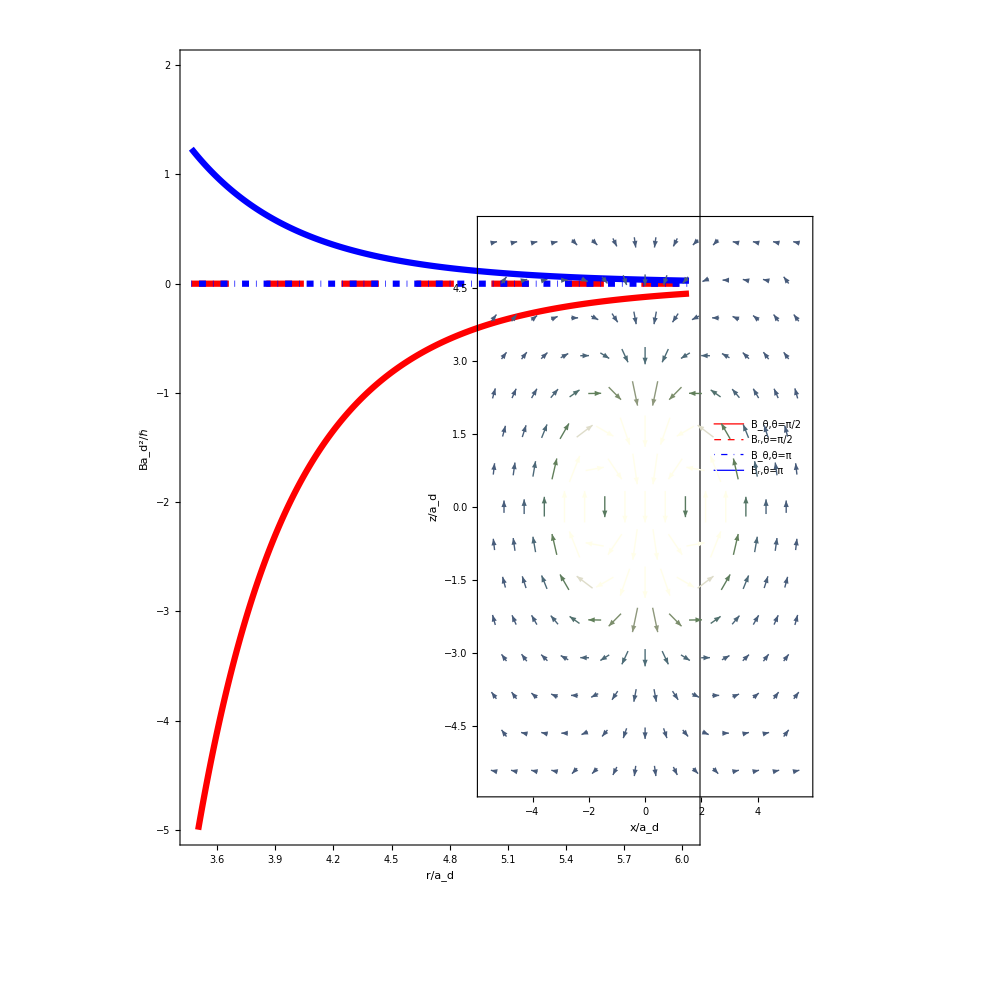

fig3a2.pdf

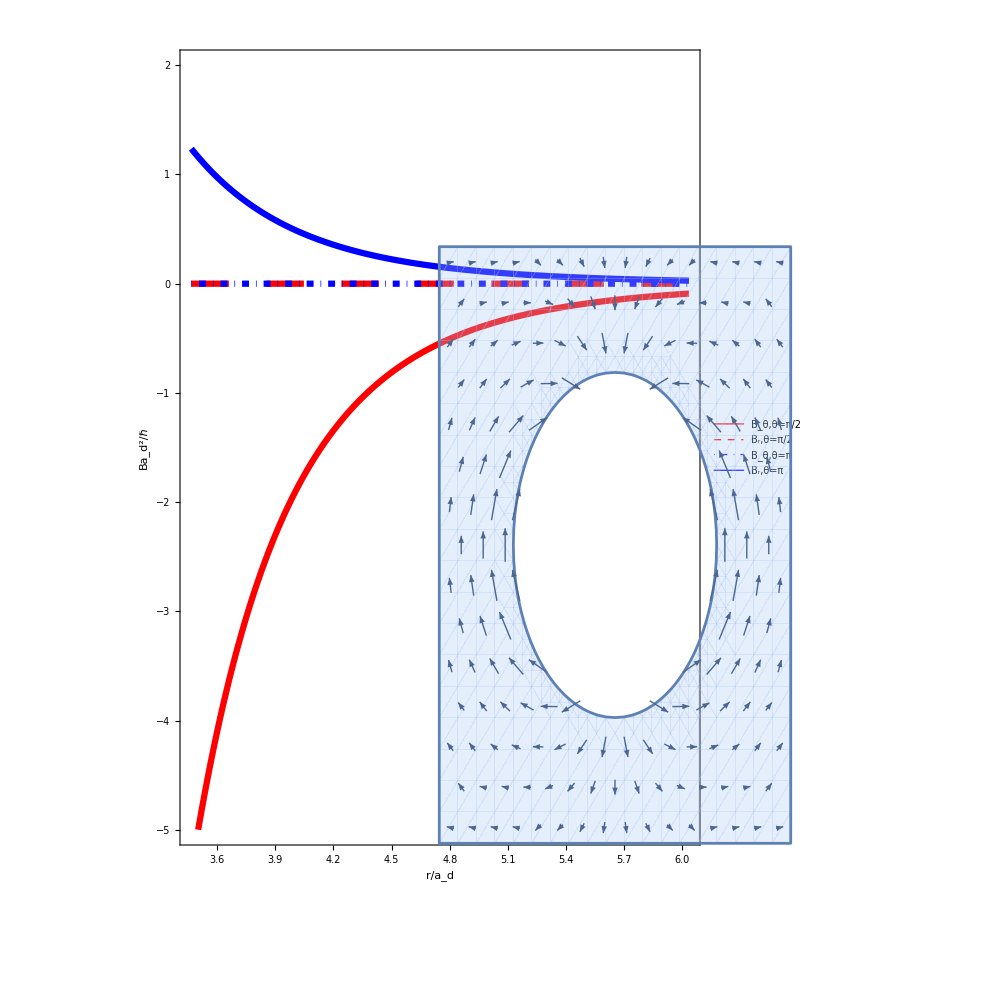

fig3a2.pdf

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

```mathematica
SFFl=ListVectorPlot[Table[{{X[[i,j]]/ad*1000,Z[[i,j]]/ad*1000},{Bx[[i,j,1]]*ad^2/10^4,Bz[[i,j,1]]*ad^2/10^4}},{i,20,Floor[Length[rval]]-100},{j,1,Length[tval]}],(*RegionFunction->Function[{X,Z},X^2+Z^2>11],*)
VectorColorFunction->"AlpineColors",VectorScaling->Automatic,VectorSizes->Medium,
Frame->True,FrameStyle->Directive[Black,16,Thickness[0.005],Bold],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->Directive[{FontSize->24,Thickness[0.005],Bold}],FrameLabel->{Style["x/a_d",FontSize->24,Thickness[0.005],Bold],Style["z/a_d",FontSize->24,Thickness[0.005],Bold]},
ImageSize->900,ImagePadding->{{120,20},{75,10}},AspectRatio->0.8];
SH=Show[Graphics[{Rectangle[{0,0},{1,1},SFl],Rectangle[{0.40,0.09},{0.83,0.82},SFFl]}],ImageSize->1000]
Export["fig3a2.pdf",SH]
```